```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(* Upper Limit for integration *)
limit = 20;

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
 
(* RawData format R, p, A, E, E + 1/R *)
(*vSg1RawData = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg1.mx"];
vSg2RawData = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg2.mx"];*)
vSg1RawData = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/s1_state.mat"][[1]];
vSg2RawData = Import["~/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/s1_state.mat"][[1]];

(* Extrapolate to R = 20 *)
vSg1Data=Table[{vSg1RawData[[i]][[1]],vSg1RawData[[i]][[5]]},{i,1,Length[vSg1RawData]}];
vSg2Data=Table[{vSg2RawData[[i]][[1]],vSg2RawData[[i]][[5]]},{i,1,Length[vSg2RawData]}];

vSg1Data=Join[vSg1Data,Table[{i,vSg1Data[[Length[vSg1Data]]][[2]]},{i,11,20,1}]];
vSg2Data=Join[vSg2Data,Table[{i,vSg2Data[[Length[vSg2Data]]][[2]]},{i,11,20,1}]];
vSg1Data
```

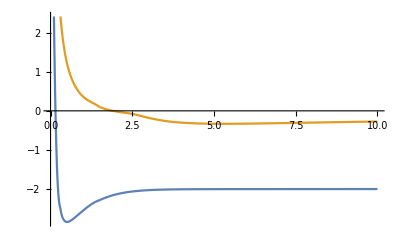
```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R","p", "A","E","E+1/r"*)
(* 1sg state, potential curve *)
Subscript[v, a]=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,2]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, b]=Interpolation[Transpose[{vSg2Data[[All,1]],vSg2Data[[All,2]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[Subscript[v, a][r]-Subscript[v, b][r]];

Plot[{Subscript[v, a][r],Subscript[v, b][r]},{r,0,10}]
-Graphics-
Interpolation::indat: "Data point \!\(\*RowBox[{\"{\", RowBox[{\"11\", \",\", RowBox[{\"{\", RowBox[{\"0.6000000000000001`\", \",\", \"0.8981464205391411`\", \",\", RowBox[{\"-\", \"35.99856474444517`\"}], \",\", RowBox[{\"-\", \"4.481483292929286`\"}], \",\", RowBox[{\"-\", \"2.8148166262626195`\"}]}], \"}\"}]}], \"}\"}]\) contains abscissa \!\(\*RowBox[{\"11\"}]\), which is not a real number."
Interpolation::indat: "Data point \!\(\*RowBox[{\"{\", RowBox[{\"11\", \",\", RowBox[{\"{\", RowBox[{\"0.6000000000000001`\", \",\", \"0.8981464205391411`\", \",\", RowBox[{\"-\", \"35.99856474444517`\"}], \",\", RowBox[{\"-\", \"4.481483292929286`\"}], \",\", RowBox[{\"-\", \"2.8148166262626195`\"}]}], \"}\"}]}], \"}\"}]\) contains abscissa \!\(\*RowBox[{\"11\"}]\), which is not a real number."
Interpolation::inord: "Value of option \!\(\*RowBox[{\"InterpolationOrder\"}]\) -> \!\(\*RowBox[{\"3.`\"}]\) should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, \!\(\*RowBox[{\"5\"}]\)."
Interpolation::inord: "Value of option \!\(\*RowBox[{\"InterpolationOrder\"}]\) -> \!\(\*RowBox[{\"3.`\"}]\) should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, \!\(\*RowBox[{\"5\"}]\)."
Interpolation::inord: "Value of option \!\(\*RowBox[{\"InterpolationOrder\"}]\) -> \!\(\*RowBox[{\"3.`\"}]\) should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, \!\(\*RowBox[{\"5\"}]\)."
General::stop: "Further output of \!\(\*StyleBox[RowBox[{\"Interpolation\", \"::\", \"inord\"}], \"MessageName\"]\) will be suppressed during this calculation."
-Graphics-
-Graphics-
```

```mathematica
(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
limit = vSg1RawData[[Length[vSg1RawData]]][[1]];
Print["limit=",limit]

(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,p1_,a1_,p2_,a2_]:=Module[{lSol1,mSol1, lSol2,mSol2,L, M, norm1, norm2},
(* 1s wavefunction *)
lSol1=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a1 +2 R λ -p1^2 λ^2)L[λ]==0 ,L[1.01]==0,L'[1.01]==1 },L[λ],{λ,1.01,limit}];
mSol1=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a1 + p1^2 μ^2)M[μ]==0, M[-0.999]==0,M'[-0.999]==1}, M[μ],{μ,-.999,.999}];
(* 2s wavefunction *) 
lSol2=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a2+2 R λ -p2^2 λ^2)L[λ]==0 ,L[1.01]==0,L'[1.01]==1 },L[λ],{λ,1.01,limit}];
mSol2=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a2 + p2^2 μ^2)M[μ]==0, M[-0.999]==0,M'[-0.999]==1}, M[μ],{μ,-.999,.999}];

(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=(NIntegrate[((L[λ]/. lSol1)(M[μ]/. mSol1))^2,{μ,-.9,.9},{λ,1.01,limit}][[1]]);
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=(NIntegrate[((L[λ]/. lSol2)(M[μ]/. mSol2))^2,{μ,-.9,.9},{λ,1.01,limit}][[1]]);
dInt=(R/2)1/Sqrt[norm1+ norm2] NIntegrate[(L[λ]/. lSol1)(M[μ]/. mSol1)λ(L[λ]/. lSol2)(M[μ]/. mSol2),{μ,-.9,.9},{λ,1.001,limit}];
{R,dInt - R/2}
];
```

```mathematica
(* Get all Rs, as and ps and calculate D(R) for all Rs *)
inputData = Transpose[{vSg1RawData[[All,1]],vSg1RawData[[All,2]],vSg1RawData[[All,3]],vSg2RawData[[All,2]],vSg2RawData[[All,3]]}];

allDR =Map[singleDR, inputData];
dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];

(* Calculate A(R)*)
a[r_]:=4/3(dR[r])^2(deltaV[r])^3/c^3 ;

solNear=Sort[Transpose[NDEigensystem[-1/(2μ)ff''[x]+(Subscript[v, a][x]-I/2 a[x])ff[x],ff,{x,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];

solFar=Sort[Transpose[NDEigensystem[-1/(2μ)ff''[x]+Subscript[v, b][x]ff[x],ff,{x,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];



fNear=solNear[[1]][[2]];
fFar = solFar[[1]][[2]];
```

kF=5.81201

kN=19484.4-19480.6 ⅈ ,Abs[kN]=27552.5

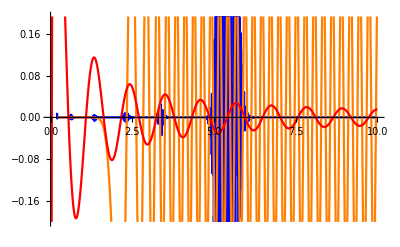

5.64259×10^-10

```mathematica
(* Now to calculate the phase shift we match the Subscript[f, R] in the region V = 0 with the solution in V = 0 , which is represented by the Bessel Functions. *)
(* Using the logarithmic derivative *)

fFar2[k_,r_]:=BesselJ[0, kF r] + BesselY[0,kF r];

logBeta[x_] := fNear'[x]/fNear[x];
```

```mathematica
(* For far away region *)
(* S wave *)
(* Derive a Bessel function at a point *)
fD[f_,l_,r_]:=N[D[f[l,x],x]/. x->r];
fD[BesselJ,0,0.13642084936916368-0.3992724676792502I]


tanPhase1[k_,r_]:=(k r fD[BesselJ,0,k r]-logBeta[r]N[BesselJ[0,k r]])/(k r fD[BesselY,0,k r]-logBeta[r]N[BesselY[0,k  r]]);
tanPhase2[k_,r_]:=(k r Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k r Sin[k  r]);

tanPhase3[k_,r_]:=(k Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k  Sin[k  r]);

kS
Table[{r,tanPhase1[kS,r]},{r,5,limit,1}] //MatrixForm
Table[{r,tanPhase2[kS,r]},{r,5,limit,1}] //MatrixForm
Table[{r,tanPhase3[kS,r]},{r,5 ,limit,1}] //MatrixForm
```

-0.0721643+0.202218 ⅈ

-0.0060197-0.00173882 ⅈ

(5 | -0.267686+0.214983 ⅈ
6 | -0.270433+0.229083 ⅈ
7 | -0.271964+0.244309 ⅈ
8 | -0.27284+0.248951 ⅈ
9 | -0.272143+0.270628 ⅈ
10 | -0.273853+0.276724 ⅈ
11 | -0.273406+0.287084 ⅈ
12 | -0.27267+0.296788 ⅈ
13 | -0.271574+0.30628 ⅈ
14 | -0.270088+0.315739 ⅈ
15 | -0.26812+0.325439 ⅈ
16 | -0.265443+0.33588 ⅈ
17 | -0.261449+0.348173 ⅈ
18 | -0.254077+0.365577 ⅈ
19 | -0.230336+0.40384 ⅈ
20 | -0.0105984-0.00619644 ⅈ)

(5 | 0.0304986+0.00866435 ⅈ
6 | 0.0367097+0.0104381 ⅈ
7 | 0.0442285+0.0122797 ⅈ
8 | 0.0466845+0.0131675 ⅈ
9 | 0.059431+0.0156786 ⅈ
10 | 0.0632307+0.017795 ⅈ
11 | 0.070263+0.0196814 ⅈ
12 | 0.077301+0.0215965 ⅈ
13 | 0.0846328+0.0235621 ⅈ
14 | 0.0924001+0.0256002 ⅈ
15 | 0.100859+0.0277504 ⅈ
16 | 0.110521+0.0300919 ⅈ
17 | 0.12258+0.0328099 ⅈ
18 | 0.14063+0.0364653 ⅈ
19 | 0.182744+0.0439333 ⅈ
20 | -7.61529+2.21387 ⅈ)

(5 | 0.030184+0.00869429 ⅈ
6 | 0.0362266+0.0104448 ⅈ
7 | 0.0424525+0.0122052 ⅈ
8 | 0.0479979+0.0138452 ⅈ
9 | 0.0547962+0.0156924 ⅈ
10 | 0.0605494+0.0174841 ⅈ
11 | 0.0666504+0.0192517 ⅈ
12 | 0.0727447+0.021024 ⅈ
13 | 0.078857+0.0228029 ⅈ
14 | 0.0849947+0.0245898 ⅈ
15 | 0.091171+0.0263871 ⅈ
16 | 0.0974115+0.0281989 ⅈ
17 | 0.103776+0.0300348 ⅈ
18 | 0.110443+0.0319222 ⅈ
19 | 0.118304+0.033997 ⅈ
20 | -7.40941+1.99344 ⅈ)